```mathematica
∑_(n=0)^(+∞) x^(2n+1)/((2n+1)!!)=∫_0^x ⅇ^(-t^2/2)ⅆt ∑_(n=0)^(+∞) x^(2n)/((2n)!!);
```

```mathematica
∑_(n=0)^(+∞) x^(2n)/((2n)!!)
```

ⅇ^(x^2/2)

```mathematica
D[∑_(n=0)^(+∞) x^(2n+1)/((2n+1)!!),x]-x ∑_(n=0)^(+∞) x^(2n+1)/((2n+1)!!)-1//Simplify
```

0

```mathematica
∑_(n=1)^(+∞) Sin[a n]/n=(π-a)/2
```

```mathematica
f[x_]:=(π-x)/2
∫_0^(2π) f[x]Cos[n x]ⅆx
∫_0^(2π) f[x]Sin[n x]ⅆx
∫_0^(2π) f[x]ⅆx
```

(Sin[n π] (-n π Cos[n π]+Sin[n π]))/n^2

(Cos[n π] (n π Cos[n π]-Sin[n π]))/n^2

0

```mathematica
((-n π Cos[n π]+Sin[n π])/n^2).
```

0

```mathematica
∑_(n=1)^∞ Sin[a n]/n//FullSimplify
```

1/2 ⅈ (-Log[1-ⅇ^(-ⅈ a)]+Log[1-ⅇ^(ⅈ a)])

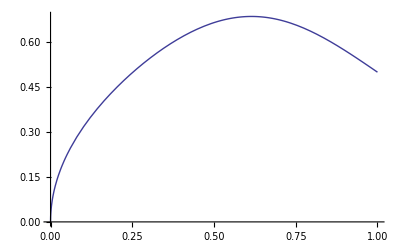

```mathematica
Plot[(√x)/(1+x^4),{x,0,1}]
```

```mathematica
∫_0^1 1/(√x)ⅆx//N
```

2.

```mathematica
Reduce[Abs[(1-x)/(1+x)]<1/50,x,Reals]
```

49/51<x<51/49

```mathematica
∑_(n=0)^(+∞) Sin[n x]/(n!)
```

ⅇ^Cos[x] Sin[Sin[x]]

```mathematica
∑_(n=0)^(+∞) (n^2-1)/((2n)!!)x^n
```

1/4 ⅇ^(x/2) (-4+2 x+x^2)

```mathematica
Series[1/4 ⅇ^(x/2) (-4+2 x+x^2),{x,0,10}]-∑_(n=0)^10 (n^2-1)/((2n)!!)x^n
```

O[x]^11